# Contractions with H_ij

```mathematica
H0ij=(π/(3(1-y)^2))(1-8y + 7y^2 - 6y^2 Log[y])((2-2y)Dij - ni nj -qi qj - qi nj + (1-2y)qj ni)
```

(π (-ni nj-nj qi-qi qj+ni qj (1-2 y)+Dij (2-2 y)) (1-8 y+7 y^2-6 y^2 Log[y]))/(3 (1-y)^2)

```mathematica
H0jk=(π/(3(1-y)^2))(1-8y + 7y^2 - 6y^2 Log[y])((2-2y)Djk - nj nk -qj qk - qj nk + (1-2y)qk nj)
```

(π (-nj nk-nk qj-qj qk+nj qk (1-2 y)+Djk (2-2 y)) (1-8 y+7 y^2-6 y^2 Log[y]))/(3 (1-y)^2)

```mathematica
H0sq = H0ij*H0jk
```

1/(9 (1-y)^4)π^2 (-ni nj-nj qi-qi qj+ni qj (1-2 y)+Dij (2-2 y)) (-nj nk-nk qj-qj qk+nj qk (1-2 y)+Djk (2-2 y)) (1-8 y+7 y^2-6 y^2 Log[y])^2

```mathematica
TraceH0sq = (Dik H0sq//Expand)/.Dij Dik Djk ->3/.Dik Djk ni nj ->1/. Dij Dik nj nk ->1/.Dik ni nj^2 nk ->1/.Dik Djk nj qi->nq/. Dik nj^2 nk qi ->nq/.Dik Djk ni qj -> nq/.Dij Dik nk qj-> nq/.Dik Djk qi qj-> 1/.Dik nj nk qi qj -> nq^2/. Dik ni nk qj^2-> 1/. Dik nk qi qj^2 -> nq/. Dij Dik nj qk -> nq/.Dik ni nj^2 qk -> nq/. Dik nj^2 qi qk ->1/. Dij Dik qj qk -> 1/. Dik ni nj qj qk -> nq^2/. Dik ni qj^2 qk -> nq/. Dik qi qj^2 qk -> 1 /. Dik ni nj nk qj -> nq /. Dik nj qi qj qk -> nq /. y-> (1-nq)/2 //FullSimplify
```

((1+nq^2) π^2 (5-2 nq-7 nq^2+6 (-1+nq)^2 Log[(1-nq)/2])^2)/(9 (1+nq)^2)

```mathematica
T2=TraceH0sq/.nq->Cos[ζ]//FullSimplify
```

(π^2 (1+Cos[ζ]^2) (5-2 Cos[ζ]-7 Cos[ζ]^2+6 (-1+Cos[ζ])^2 Log[Sin[ζ/2]^2])^2)/(9 (1+Cos[ζ])^2)

```mathematica
TeXForm[T2]
```

\frac{\pi ^2 \left(\cos ^2(\zeta )+1\right) \left(-7 \cos ^2(\zeta )-2
   \cos (\zeta )+6 (\cos (\zeta )-1)^2 \log \left(\sin
   ^2\left(\frac{\zeta }{2}\right)\right)+5\right)^2}{9 (\cos (\zeta
   )+1)^2}

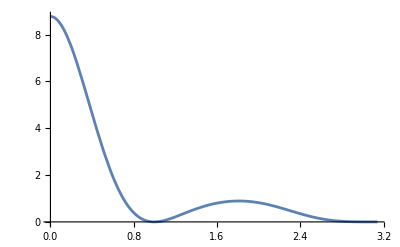

```mathematica
Plot[T2,{ζ,0.001,π-0.001},PlotRange->All]
```

```mathematica
FindRoot[T2==0.89, {ζ,2}]
```

{ζ→1.84405}

```mathematica
Sqrt[((1+nq^2) π^2 (5-2 nq-7 nq^2+6 (-1+nq)^2 Log[(1-nq)/2])^2)/(9 (1+nq)^2)]
```

1/3 π √(((1+nq^2) (5-2 nq-7 nq^2+6 (-1+nq)^2 Log[(1-nq)/2])^2)/(1+nq)^2)

```mathematica
TraceH0sq/.nq->1+ϵ//Simplify
```

(π^2 (2+2 ϵ+ϵ^2) (4+16 ϵ+7 ϵ^2-6 ϵ^2 Log[-ϵ/2])^2)/(9 (2+ϵ)^2)

```mathematica
Normal[Series[TraceH0sq/.nq->1-ϵ,{ϵ,0,2}]]
```

(8 π^2)/9-(64 π^2 ϵ)/9+2/9 π^2 ϵ^2 (79+12 Log[2]-12 Log[ϵ])

```mathematica
FindRoot[TraceH0sq==0, {nq,0}]
```

{nq→0.543051}

```mathematica
FindInstance[{TraceH0sq==8.21042,-1<=nq<=1}, nq,1]
```

{{nq→0.991677}}

```mathematica
Solve[{TraceH0sq==0.00121246,-1<=nq<=1}, nq]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{nq→-0.988103},{nq→0.53228},{nq→0.553509}}

```mathematica
a1=8π(Av)y((3 y^2 Log[y]/(y-1)) - 4y +1)/(3 AA CC)
```

(8 Av π y (1-4 y+(3 y^2 Log[y])/(-1+y)))/(3 AA CC)

```mathematica
a2=8π(Av)y((3 y^2 Log[y]/(y-1)) - 4y +1)/(3 AA BB)
```

(8 Av π y (1-4 y+(3 y^2 Log[y])/(-1+y)))/(3 AA BB)

```mathematica
a3=-8π y^2( (y-1)(2y+1) - 3y Log[y] )(2 nv (y-1) - Sqrt[4 (nv^2 - 1)(y-1)y - Av^2])/(3 AA^2 (y-1))
```

-(8 π y^2 (2 nv (-1+y)-√(-Av^2+4 (-1+nv^2) (-1+y) y)) ((-1+y) (1+2 y)-3 y Log[y]))/(3 AA^2 (-1+y))

```mathematica
a4=8π y^2( (y-1)(2y+1) - 3y Log[y] )( 2 nv Sqrt[1-y] + Sqrt[ ((Av^2)/(y-1)) +4 (nv^2 - 1)y ])/(3 BB CC Sqrt[1-y])
```

(8 π y^2 (2 nv √(1-y)+√(Av^2/(-1+y)+4 (-1+nv^2) y)) ((-1+y) (1+2 y)-3 y Log[y]))/(3 BB CC √(1-y))

```mathematica
(H1ij = a1 Ai Cj +a2 Bi Aj + a3 Ai Aj + a4 Bi Cj)
```

(8 Bi Cj π y^2 (2 nv √(1-y)+√(Av^2/(-1+y)+4 (-1+nv^2) y)) ((-1+y) (1+2 y)-3 y Log[y]))/(3 BB CC √(1-y))-(8 Ai Aj π y^2 (2 nv (-1+y)-√(-Av^2+4 (-1+nv^2) (-1+y) y)) ((-1+y) (1+2 y)-3 y Log[y]))/(3 AA^2 (-1+y))+(8 Aj Av Bi π y (1-4 y+(3 y^2 Log[y])/(-1+y)))/(3 AA BB)+(8 Ai Av Cj π y (1-4 y+(3 y^2 Log[y])/(-1+y)))/(3 AA CC)

```mathematica
(H1jk = a1 Aj Ck+a2 Bj Ak + a3 Aj Ak + a4 Bj Ck)
```

(8 Bj Ck π y^2 (2 nv √(1-y)+√(Av^2/(-1+y)+4 (-1+nv^2) y)) ((-1+y) (1+2 y)-3 y Log[y]))/(3 BB CC √(1-y))-(8 Aj Ak π y^2 (2 nv (-1+y)-√(-Av^2+4 (-1+nv^2) (-1+y) y)) ((-1+y) (1+2 y)-3 y Log[y]))/(3 AA^2 (-1+y))+(8 Ak Av Bj π y (1-4 y+(3 y^2 Log[y])/(-1+y)))/(3 AA BB)+(8 Aj Av Ck π y (1-4 y+(3 y^2 Log[y])/(-1+y)))/(3 AA CC)

```mathematica
H1sq=H1ij*H1jk
```

((8 Bi Cj π y^2 (2 nv √(1-y)+√(Av^2/(-1+y)+4 (-1+nv^2) y)) ((-1+y) (1+2 y)-3 y Log[y]))/(3 BB CC √(1-y))-(8 Ai Aj π y^2 (2 nv (-1+y)-√(-Av^2+4 (-1+nv^2) (-1+y) y)) ((-1+y) (1+2 y)-3 y Log[y]))/(3 AA^2 (-1+y))+(8 Aj Av Bi π y (1-4 y+(3 y^2 Log[y])/(-1+y)))/(3 AA BB)+(8 Ai Av Cj π y (1-4 y+(3 y^2 Log[y])/(-1+y)))/(3 AA CC)) ((8 Bj Ck π y^2 (2 nv √(1-y)+√(Av^2/(-1+y)+4 (-1+nv^2) y)) ((-1+y) (1+2 y)-3 y Log[y]))/(3 BB CC √(1-y))-(8 Aj Ak π y^2 (2 nv (-1+y)-√(-Av^2+4 (-1+nv^2) (-1+y) y)) ((-1+y) (1+2 y)-3 y Log[y]))/(3 AA^2 (-1+y))+(8 Ak Av Bj π y (1-4 y+(3 y^2 Log[y])/(-1+y)))/(3 AA BB)+(8 Aj Av Ck π y (1-4 y+(3 y^2 Log[y])/(-1+y)))/(3 AA CC))

```mathematica
Trace1=((Dik H1sq//Expand)/. Dik Aj Ak Bi Bj -> AB^2/. Dik Ai Ak Bj Cj -> AA BC/. Dik Aj^2 Bi Ck -> AA BC/. Dik Aj Ak Bi Cj -> AC AB/. Dik Ai Aj Bj Ck -> AB AC/. Dik Ai Aj Cj Ck -> AC^2/. Dik Ak Bi Bj Cj -> AB BC/. Dik Aj Bi Bj Ck -> AB BC /. Dik Aj Bi Cj Ck -> AC BC/. Dik Ai Bj Cj Ck -> AC BC/. Dik Aj^2 Ak Bi -> AA AB /. Dik Ai Aj Ak Bj -> AA AB /. Dik Ai Aj Ak Cj -> AA AC/. Dik Ai Aj^2 Ck -> AA AC /. Dik Bi Bj Cj Ck -> BC^2/. Dik Ai Aj^2 Ak -> AA^2)//FullSimplify
```

-1/(9 AA^2 BB^2 CC^2 (1-y)^(5/2))64 π^2 y^2 ((-1+y)^2 (-AC^2 Av^2 BB^2 (1-4 y)^2 √(1-y)-2 AA Av BC CC (-1+4 y) (Av BB √(1-y) (-1+4 y)-AB (-1+y) y (1+2 y) (2 nv √(1-y)+√(Av^2/(-1+y)+4 (-1+nv^2) y)))-AA^2 BC^2 y^2 (1+2 y)^2 (-Av^2 √(1-y)+4 (-1+y) (-nv^2 √(1-y)+√(1-y) y+nv (-1+y) √(Av^2/(-1+y)+4 (-1+nv^2) y)))+2 AC BB y (1+2 y) (AA Av BC (-1+y) (-1+4 y) (2 nv √(1-y)+√(Av^2/(-1+y)+4 (-1+nv^2) y))+CC (-2 nv (-1+y)+√(-Av^2+4 (-1+nv^2) (-1+y) y)) (Av BB √(1-y) (-1+4 y)-AB (-1+y) y (1+2 y) (2 nv √(1-y)+√(Av^2/(-1+y)+4 (-1+nv^2) y))))+CC^2 √(1-y) (-AB^2 Av^2 (1-4 y)^2+2 AB Av BB y (-1+2 y+8 y^2) (2 nv-2 nv y+√(-Av^2+4 (-1+nv^2) (-1+y) y))+BB^2 y^2 (1+2 y)^2 (Av^2+4 (-1+y) (y+nv (nv-2 nv y+√(-Av^2+4 (-1+nv^2) (-1+y) y))))))-6 (-1+y) y^2 (AC^2 Av^2 BB^2 (1-4 y) √(1-y)+AA Av BC CC (2 Av BB (1-4 y) √(1-y)+AB (-1+y) (-1+y (5+2 y)) (2 nv √(1-y)+√(Av^2/(-1+y)+4 (-1+nv^2) y)))-AA^2 BC^2 y (1+2 y) (-Av^2 √(1-y)+4 (-1+y) (-nv^2 √(1-y)+√(1-y) y+nv (-1+y) √(Av^2/(-1+y)+4 (-1+nv^2) y)))+AC BB (AA Av BC (-1+y) (-1+y (5+2 y)) (2 nv √(1-y)+√(Av^2/(-1+y)+4 (-1+nv^2) y))+CC (-2 nv (-1+y)+√(-Av^2+4 (-1+nv^2) (-1+y) y)) (Av BB √(1-y) (-1+y (5+2 y))-2 AB (-1+y) y (1+2 y) (2 nv √(1-y)+√(Av^2/(-1+y)+4 (-1+nv^2) y))))+CC^2 √(1-y) (AB^2 Av^2 (1-4 y)+AB Av BB (-1+y (5+2 y)) (2 nv-2 nv y+√(-Av^2+4 (-1+nv^2) (-1+y) y))+BB^2 y (1+2 y) (Av^2+4 (-1+y) (y+nv (nv-2 nv y+√(-Av^2+4 (-1+nv^2) (-1+y) y)))))) Log[y]+9 y^4 (-AC^2 Av^2 BB^2 √(1-y)-2 AA Av BC CC (Av BB √(1-y)-AB (-1+y) (2 nv √(1-y)+√(Av^2/(-1+y)+4 (-1+nv^2) y)))+AA^2 BC^2 (Av^2 √(1-y)-4 (-1+y) (-nv^2 √(1-y)+√(1-y) y+nv (-1+y) √(Av^2/(-1+y)+4 (-1+nv^2) y)))+2 AC BB (AA Av BC (-1+y) (2 nv √(1-y)+√(Av^2/(-1+y)+4 (-1+nv^2) y))+CC (-2 nv (-1+y)+√(-Av^2+4 (-1+nv^2) (-1+y) y)) (Av BB √(1-y)-AB (-1+y) (2 nv √(1-y)+√(Av^2/(-1+y)+4 (-1+nv^2) y))))+CC^2 √(1-y) (-AB^2 Av^2+2 AB Av BB (2 nv-2 nv y+√(-Av^2+4 (-1+nv^2) (-1+y) y))+BB^2 (Av^2+4 (-1+y) (y+nv (nv-2 nv y+√(-Av^2+4 (-1+nv^2) (-1+y) y)))))) Log[y]^2)

```mathematica
TrH1H1=(Trace1/. AA-> 1-nq^2/. BB-> 1-nq^2/. CC-> 1-nq^2/. AB->0/. BC->nq (nq^2-1)/. AC-> 0 )//FullSimplify
```

-1/(9 (-1+nq^2)^2 (1-y)^(5/2))64 π^2 y^2 ((-1+y)^2 (Av^2 √(1-y) (2 nq (1-4 y)^2+y^2 (1+2 y)^2+nq^2 y^2 (1+2 y)^2)-4 (-1+y) y^2 (1+2 y)^2 ((-1+nq^2) √(1-y) y+nv^2 √(1-y) (-1-nq^2+2 y)+nq^2 nv (-1+y) √(Av^2/(-1+y)+4 (-1+nv^2) y)-nv √(1-y) √(-Av^2+4 (-1+nv^2) (-1+y) y)))-6 (-1+y) y^2 (Av^2 √(1-y) (-2 nq+y+nq (8+nq) y+2 (1+nq^2) y^2)-4 (-1+y) y (1+2 y) ((-1+nq^2) √(1-y) y+nv^2 √(1-y) (-1-nq^2+2 y)+nq^2 nv (-1+y) √(Av^2/(-1+y)+4 (-1+nv^2) y)-nv √(1-y) √(-Av^2+4 (-1+nv^2) (-1+y) y))) Log[y]+9 y^4 (Av^2 (1+nq)^2 √(1-y)-4 (-1+y) ((-1+nq^2) √(1-y) y+nv^2 √(1-y) (-1-nq^2+2 y)+nq^2 nv (-1+y) √(Av^2/(-1+y)+4 (-1+nv^2) y)-nv √(1-y) √(-Av^2+4 (-1+nv^2) (-1+y) y))) Log[y]^2)

```mathematica
Eq1= Collect[TrH1H1,{ nq^2 nv (-1+y) √(Av^2/(-1+y)+4 (-1+nv^2) y)-nv √(1-y) √(-Av^2+4 (-1+nv^2) (-1+y) y),nv^2 (1+nq^2-2 y)+y-nq^2 y, Av^2 },FullSimplify]/.nq^2 nv (-1+y) √(Av^2/(-1+y)+4 (-1+nv^2) y)-nv √(1-y) √(-Av^2+4 (-1+nv^2) (-1+y) y)-> β/. nv^2 (1+nq^2-2 y)+y-nq^2 y->γ/. -(-1+y)^2 (2 nq (1-4 y)^2+y^2 (1+2 y)^2+nq^2 y^2 (1+2 y)^2)+6 (-1+y) y^2 (-2 nq+y+nq (8+nq) y+2 (1+nq^2) y^2) Log[y]-9 (1+nq)^2 y^4 Log[y]^2->α/. 1+y-2 y^2+3 y Log[y]->δ//FullSimplify
```

(64 π^2 (Av^2 √(1-y) y^2 α+4 (-1+y) y^4 (β-√(1-y) γ) δ^2))/(9 (-1+nq^2)^2 (1-y)^(5/2))

```mathematica
α1 = -(-1+y)^2 (2 nq (1-4 y)^2+y^2 (1+2 y)^2+nq^2 y^2 (1+2 y)^2)+6 (-1+y) y^2 (-2 nq+y+nq (8+nq) y+2 (1+nq^2) y^2) Log[y]-9 (1+nq)^2 y^4 Log[y]^2 //FullSimplify
```

-(-1+y)^2 (2 nq (1-4 y)^2+y^2 (1+2 y)^2+nq^2 y^2 (1+2 y)^2)+6 (-1+y) y^2 (-2 nq+y+nq (8+nq) y+2 (1+nq^2) y^2) Log[y]-9 (1+nq)^2 y^4 Log[y]^2

```mathematica
TeXForm[α1 ]
```

-(y-1)^2 \left(\text{nq}^2 y^2 (2 y+1)^2+2 \text{nq} (1-4 y)^2+y^2 (2
   y+1)^2\right)+6 (y-1) y^2 \left(2 \left(\text{nq}^2+1\right)
   y^2+\text{nq} (\text{nq}+8) y-2 \text{nq}+y\right) \log (y)-9
   (\text{nq}+1)^2 y^4 \log ^2(y)

```mathematica
β1 = nq^2 nv (-1+y) √(Av^2/(-1+y)+4 (-1+nv^2) y)-nv √(1-y) √(-Av^2+4 (-1+nv^2) (-1+y) y)
```

nq^2 nv (-1+y) √(Av^2/(-1+y)+4 (-1+nv^2) y)-nv √(1-y) √(-Av^2+4 (-1+nv^2) (-1+y) y)

```mathematica
TeXForm[β1]
```

\text{nq}^2 \text{nv} (y-1) \sqrt{\frac{\text{Av}^2}{y-1}+4
   \left(\text{nv}^2-1\right) y}-\text{nv} \sqrt{1-y} \sqrt{4
   \left(\text{nv}^2-1\right) (y-1) y-\text{Av}^2}

```mathematica
γ1 = nv^2 (1+nq^2-2 y)+y-nq^2 y //FullSimplify
```

nv^2 (1+nq^2-2 y)+y-nq^2 y

```mathematica
TeXForm[γ1]
```

\text{nv}^2 \left(\text{nq}^2-2 y+1\right)+\text{nq}^2 (-y)+y

```mathematica
TeXForm[Eq1]
```

\frac{64 \pi ^2 \left(\alpha  \text{Av}^2 \sqrt{1-y} y^2+4 \delta ^2
   (y-1) y^4 \left(\beta -\gamma  \sqrt{1-y}\right)\right)}{9
   \left(\text{nq}^2-1\right)^2 (1-y)^{5/2}}

```mathematica
(TraceHij=(Dij H1ij //Expand)/.Dij Ai Cj->AC /.Dij Bi Aj->AB/. Dij Ai Aj->AA /. Dij Bi Cj->BC/. AA-> 1-nq^2/. BB-> 1-nq^2/. CC->  1-nq^2/. AB->0/. BC->nq (nq^2-1)/. AC-> 0 )//Expand//FullSimplify
```

-1/(3 (-1+nq^2) (1-y)^(3/2))8 π y^2 (-2 (1+nq) nv (1-y)^(3/2)+nq (-1+y) √(Av^2/(-1+y)+4 (-1+nv^2) y)-√(1-y) √(-Av^2+4 (-1+nv^2) (-1+y) y)) ((-1+y) (1+2 y)-3 y Log[y])

```mathematica
Collect[TraceHij,{  (1-y)^(3/2)},FullSimplify]/.(-1+y) (1+2 y)-3 y Log[y] ->F0
```

-(8 F0 nq π √(1-y) y^2 √(Av^2/(-1+y)+4 (-1+nv^2) y))/(3 (-1+nq^2) (-1+y))-(8 F0 π y^2 (-2 (1+nq) nv (-1+y)+√(-Av^2+4 (-1+nv^2) (-1+y) y)))/(3 (-1+nq^2) (-1+y))

## Special elections for q in the ,

## Case:

```mathematica
EqnV= (TrH1H1/. nq-> -vq/. nv^2->1/. nv ->-1/.Av->0/. y-> (1+vq)/2 )//FullSimplify
```

(4 π^2 (1+vq)^2 (1+vq^2) (-2+Log[8]+vq (1+vq+Log[8])-3 (1+vq) Log[1+vq])^2)/(9 (-1+vq)^2)

```mathematica
M2=(4 π^2 (1+vq)^2 (1+vq^2) (-2+Log[8]+vq (1+vq+Log[8])-3 (1+vq) Log[1+vq])^2)/(9 (-1+vq)^2)/.vq->-Cos[ζ] //FullSimplify
```

(4 π^2 (-1+Cos[ζ])^2 (1+Cos[ζ]^2) (-2-Cos[ζ]+Cos[ζ]^2+Log[8]-Cos[ζ] Log[8]+3 (-1+Cos[ζ]) Log[1-Cos[ζ]])^2)/(9 (1+Cos[ζ])^2)

```mathematica
TeXForm[M2]
```

\frac{4 \pi ^2 (\cos (\zeta )-1)^2 \left(\cos ^2(\zeta )+1\right)
   \left(\cos ^2(\zeta )-\cos (\zeta )-\log (8) \cos (\zeta )+3 (\cos
   (\zeta )-1) \log (1-\cos (\zeta ))-2+\log (8)\right)^2}{9 (\cos
   (\zeta )+1)^2}

```mathematica
FindRoot[(-2+Log[8]+Cos[ζ] (1+Cos[ζ]+Log[8])-3 (1+Cos[ζ]) Log[1+Cos[ζ]])==0,{ζ,2}]
```

{ζ→1.86504}

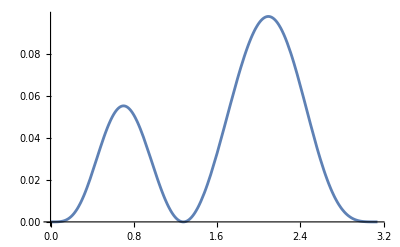

```mathematica
Plot[M2,{ζ,0,π},PlotRange->All]
```

```mathematica
FindRoot[M2==0.098, {ζ,2}]
```

{ζ→2.08485}

```mathematica
degrees = (2.0848545164455*180)/π
```

119.453

```mathematica
FindRoot[EqnV==0, {vq,0}]
```

{vq→-0.290015}

```mathematica
Solve[{EqnV==0.000305446, -1<=vq<=1}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{vq→-0.993784},{vq→-0.317515},{vq→-0.262216},{vq→0.987984}}

```mathematica
Solve[{EqnV==0.0948869, -1<=vq<=1}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{vq→0.419003},{vq→0.573974}}

```mathematica
Maximize[{Sol1,-1<vq<=1},vq, Reals]
```

{Sol1,{vq→-8/17}}

## Case:

```mathematica
EqV= (TrH1H1/. nq-> vq/. nv^2->1/. nv ->1/.Av->0/. y-> (1-vq)/2)//FullSimplify
```

(4 π^2 (-1+vq)^2 (1+vq^2) (-2+(-1+vq) vq+Log[8]+3 vq Log[(1-vq)/2]-3 Log[1-vq])^2)/(9 (1+vq)^2)

```mathematica
M2=EqV/.vq->Cos[ζ]//FullSimplify
```

1/18 π^2 (3+Cos[2 ζ]) (-3+Cos[2 ζ]+Log[64]-6 Log[1-Cos[ζ]]+Cos[ζ] (-2+6 Log[Sin[ζ/2]^2]))^2 Tan[ζ/2]^4

```mathematica
Solve[{EqV==0.000305446, -1<=vq<=1}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{vq→-0.987984},{vq→0.262216},{vq→0.317515},{vq→0.993784}}

```mathematica
Solve[{EqV==0.0948869, -1<=vq<=1}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{vq→-0.573974},{vq→-0.419003}}

## Case: (This means n orthogonal to v)

```mathematica
EqnV0= (TrH1H1/. nv ->0/. y-> (1-nq)/2)//FullSimplify
```

1/(9 (1+nq)^2)4 π^2 ((1+nq) ((-2+nq)^2 (-1+nq)^4 (1+nq)-Av^2 (4+(-1+nq) nq (8+nq (15+(-6+nq) nq))))+6 (-1+nq)^2 ((-2+nq) (-1+nq)^3 (1+nq)+Av^2 (-2+nq+4 nq^2-nq^3)) Log[(1-nq)/2]+9 (-1+nq)^4 (-1-Av+nq) (-1+Av+nq) Log[(1-nq)/2]^2)

```mathematica
FindRoot[EqnV0==0, {nq,0}]
```

FindRoot::nlnum: The function value {4.38649 (4.32408 (-1.-1. Av) (-1.+Av)+1. (4.-4. Av^2)-4.15888 (2.-2. Av^2))} is not a list of numbers with dimensions {1} at {nq} = {0.}.

FindRoot[EqnV0==0,{nq,0}]

## Special elections for q in the ,

## Case:

## Case:

## Case: